```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210421_OR_model_and_other_lines_sliding"];
```

```mathematica
datafull=Import["../data/CSP_num.csv",HeaderLines->2];
datafull[[1]]
Dimensions@datafull
```

{1660,CCM1,17078201-01,239846,49,17078201,5,1240,16.766,10.466,66,6.45848,30.06.17 20:11}

{212902,13}

```mathematica
nullpos=Position[datafull[[All,8]],_?(Head@#==String&)];
datafull=Delete[datafull,nullpos];
```

```mathematica
mostlyzeropos=Position[datafull[[All,9]],_?(#==0&)][[{2,3}]];
datafull=Delete[datafull,mostlyzeropos];
```

```mathematica
deletepos=Position[datafull[[All,11]],_?(1500<#&)];
(* Position[datafull[[All,8]],_?(35000<#&)] *)
datafull=Delete[datafull,deletepos];
```

```mathematica
deletepos2=Position[datafull[[All,11]],_?(10>#&)];
(* Position[datafull[[All,8]],_?(200>#&)] *)
datafull=Delete[datafull,deletepos2];
```

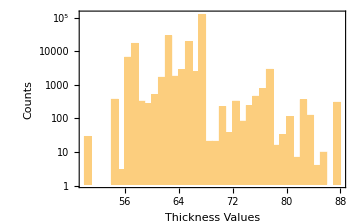
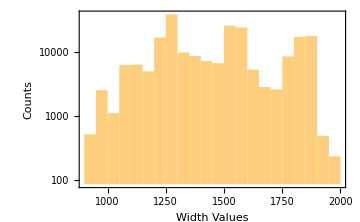

```mathematica
{Histogram[datafull[[All,11]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafull[[All,8]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium]}
```

```mathematica
(* marginal density rows deletion *)
datafull=Delete[datafull,{{28855},{196519},{11398},{44971},{67986}}];
```

```mathematica
(* remained negative density rows deletion *)
datafull=Delete[datafull,{{80527},{82593},{86698},{88884},{98206},{98207},{159853},{159854},{172604},{172605},{172606},{184960},{189744},{189752},{195041},{195976},{199764},{200365},{200740},{200741},{200993},{200994},{200995},{201012},{201566},{201581},{201582},{201584},{201589},{201591},{201593},{201594},{201604},{201606},{202974},{204090},{204869}}];
```

irrelevant density rows deletion

```mathematica
datafull=Delete[datafull,{{291},{598},{781},{782},{784},{787},{792},{793},{796},{801},{803},{805},{806},{807},{808},{812},{813},{814},{815},{817},{818},{822},{823},{824},{826},{2451},{2482},{2629},{4308},{4679},{4759},{5426},{5427},{5428},{5429},{5430},{5431},{5432},{5588},{5589},{7408},{7409},{7410},{7934},{8739},{8916},{8917},{8918},{9269},{9859},{10486},{10682},{10683},{11396},{11845},{11846},{11899},{11900},{12808},{12809},{15221},{16218},{16810},{16946},{17060},{17989},{18848},{19118},{19129},{19130},{19359},{19360},{19671},{20648},{20649},{22398},{22445},{22446},{24461},{24462},{24463},{26053},{26685},{26840},{27007},{28023},{28198},{28205},{28219},{28297},{28312},{29593},{29962},{31296},{31897},{32703},{33092},{33093},{33094},{33095},{33096},{33097},{33128},{33959},{35602},{35653},{36926},{36927},{37026},{37692},{37871},{39185},{39186},{39187},{39188},{39189},{40389},{41519},{41798},{41799},{41800},{41801},{41802},{41803},{41804},{41805},{42738},{43252},{43254},{43257},{43258},{43876},{44301},{46452},{46839},{46857},{46858},{46859},{46860},{46861},{46862},{47066},{47918},{47919},{48345},{49609},{49611},{50363},{50364},{50365},{50776},{53737},{53738},{54306},{54307},{54709},{55854},{56474},{56476},{56481},{56482},{56483},{56484},{56485},{56486},{56487},{56489},{56491},{56492},{56494},{56495},{56497},{56499},{56500},{56506},{56507},{56508},{56511},{57140},{57534},{58575},{58576},{58577},{58579},{58582},{58583},{58584},{58585},{58586},{58587},{59789},{61116},{64390},{64525},{64526},{64532},{66295},{66296},{66895},{66896},{66897},{66898},{66899},{66900},{66901},{66902},{66903},{66904},{66905},{66906},{68949},{70486},{70699},{70836},{70837},{70838},{70839},{70840},{70841},{70842},{71408},{72655},{72656},{72657},{72658},{74734},{74735},{74737},{74822},{76949},{76950},{77155},{78893},{78894},{78895},{78896},{78897},{78898},{80639},{80640},{80641},{80642},{80643},{80644},{82591},{84966},{85897},{87074},{87076},{87161},{87162},{87163},{96818},{97416},{98124},{98138},{98139},{98140},{98141},{98164},{98175},{98186},{98192},{98193},{98200},{99458},{99459},{101423},{101424},{101425},{101753},{101754},{102671},{103825},{105730},{106162},{109857},{112218},{112219},{112221},{112222},{112225},{112226},{112227},{112228},{112232},{114053},{114075},{114076},{114077},{114078},{117572},{117649},{117705},{121153},{123748},{124169},{126981},{127255},{127256},{127257},{127258},{130460},{131044},{133125},{133133},{154118},{155816},{158377},{165600},{165615},{165617},{165618},{165633},{165953},{172592},{172593},{172594},{172595},{173320},{174236},{177986},{188289},{188296},{191651},{197105},{199867},{200694},{200771},{201536},{201537},{201539},{201540},{201541},{201542},{201543},{201546},{201547},{201548},{201549},{201550},{201551},{201552},{201553},{201554},{201555},{201563},{201565},{201566},{201568},{201569},{202940},{202941},{204485},{212656},{212692},{212694}}];
```

```mathematica
density[thick_,width_,length_,weight_]:=N@weight/(thick*width*length);
```

```mathematica
thickvaluesthkpos=datafull[[All,11]];
widthvaluesthkpos=datafull[[All,8]];
lengthvaluesthkpos=datafull[[All,9]];
weightvaluesthkpos=datafull[[All,10]];
densities=Quiet@Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],lengthvaluesthkpos[[i]],weightvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.{Indeterminate->0.,ComplexInfinity->0.};
KeySort@Counts@densities
```

<|0.→968,6.6087×10^-6→1,6.64335×10^-6→1,6.71005×10^-6→1,6.74438×10^-6→1,6.75775×10^-6→1,134194,8.46405×10^-6→1,8.47798×10^-6→1,8.48358×10^-6→1,8.57632×10^-6→1,8.58354×10^-6→1|>
 |  |  |  |

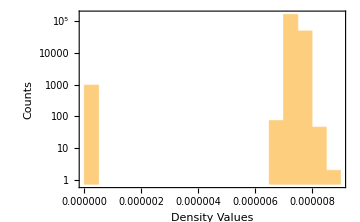

```mathematica
Histogram[densities,ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Density Values","Counts"},ImageSize->Medium]
```

```mathematica
datafull=datafull[[Flatten@Position[densities,_?(#≠0&)]]];
```

```mathematica
thickvaluesthkpos=datafull[[All,11]];
widthvaluesthkpos=datafull[[All,8]];
lengthvaluesthkpos=datafull[[All,9]];
weightvaluesthkpos=datafull[[All,10]];
densities=Quiet@Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],lengthvaluesthkpos[[i]],weightvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.{Indeterminate->0.,ComplexInfinity->0.};
```

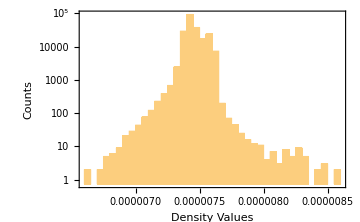

```mathematica
Histogram[densities,ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Density Values","Counts"},ImageSize->Medium]
```

```mathematica
Length@datafull
```

211512

```mathematica
secondscolumn=Table[AbsoluteTime[{datafull[[i,13]],{"Day",".","Month",".","YearShort"," ","Hour",":","Minute"}}],{i,Length@datafull}];
datafull=Join[datafull,Partition[secondscolumn,1],2];
datafullsorted=Sort[datafull,#1[[1]]<#2[[1]]&];
```

```mathematica
(* checking if sequences are revealing consecutive *)
Length@Table[DeleteDuplicates@i,{i,Split[datafullsorted[[All,1]],#2==#1&]}]
Length@DeleteDuplicates[datafullsorted[[All,1]]]
```

1587

1587

Deletion of sequences less than 50

```mathematica
deletepos5=Flatten@Table[Position[datafullsorted[[All,1]],i],{i,Keys@Cases[Normal@Counts@datafullsorted[[All,1]],_?(Values[#]<50&)]}];
datafullsorted=Delete[datafullsorted,Partition[deletepos5,1]];
```

```mathematica
Dimensions@datafullsorted
```

{205496,14}

```mathematica
programids=DeleteDuplicates@datafullsorted[[All,1]];
Length@programids
datafullsortedfinal=Flatten[Table[Sort[Select[datafullsorted,#[[1]]==i&],#1[[14]]<#2[[14]]&],{i,programids}],1];
Dimensions@datafullsortedfinal
```

1357

{205496,14}

```mathematica
datafullsortedfinal[[1]]
```

{1660,CCM1,17078201-01,239846,49,17078201,5,1240,16.766,10.466,66,6.45848,30.06.17 20:11,3707842260}

```mathematica
data=Join[Partition[Range@Length@datafullsortedfinal,1],Partition[datafullsortedfinal[[All,1]],1],ConstantArray[{0,0,0,0,0,0},Length@datafullsortedfinal],datafullsortedfinal[[All,{8,11,13,14}]],2]
```

{{1,1660,0,0,0,0,0,0,1240,66,30.06.17 20:11,3707842260},{2,1660,0,0,0,0,0,0,1229,65,30.06.17 20:19,3707842740},205492,{205495,9X0007,0,0,0,0,0,0,1278,67,21.09.19 00:42,3778015320},{205496,9X0007,0,0,0,0,0,0,1278,67,21.09.19 00:51,3778015860}}
 |  |  |  |

```mathematica
Dimensions@data
```

{205496,12}

```mathematica
(* Export["csp_manipulated_205496.csv",data] *)
```